## Full Datasets (By year)

```mathematica
(*Data for distance ladder dependent measurements with uncertainties handled by Around,excluding SH0ES 2022*)distanceLadderDependent={{2019.0,Around[73.3,4.0]},{2020.0,Around[76.0,3.4]},{2021.0,Around[73.3,3.1]},{2021.1,Around[69.8,2.3]},{2021.2,Around[73.04,1.04]},{2022.0,Around[76.94,6.4]},{2022.1,Around[74.82,1.81]},{2022.2,Around[70.92,2.63]},{2022.3,Around[73.1,2.5]},{2023.0,Around[73.22,2.06]},{2023.1,Around[71.76,1.32]},{2023.2,Around[73.22,1.45]},{2023.3,Around[74.1,8]},{2023.4,Around[72.37,2.97]},{2024.0,Around[73.1,2.3]},{2024.1,Around[74.7,3.1]},{2024.2,Around[68.00,2.7]},{2024.3,Around[72.05,3.6]},{2024.4,Around[73.3,4.08]},{2024.5,Around[76.05,4.90]}};

distanceLadderIndependent={{2003.00,Around[61,18]},{2013.00,Around[68,9]},{2015.00,Around[66.0,6.0]},{2019.00,Around[74.2,1.6]},{2020.00,Around[73.9,3.0]},{2020.05,Around[67.4,4]},{2021.00,Around[68.0,7]},{2021.05,Around[64.67,5.14]},{2022.00,Around[64.8,2.4]},{2022.05,Around[65.9,3.0]},{2022.10,Around[69.6,5.5]},{2023.00,Around[66.7,5.3]},{2023.05,Around[72.9,2.15]},{2023.10,Around[71.5,3.7]},{2023.15,Around[71.5,3.1]},{2023.20,Around[85.4,31.5]},{2023.25,Around[75.46,5.365]},{2023.30,Around[62.4,4.0]},{2023.35,Around[67.0,3.6]},{2023.40,Around[59.1,3.55]},{2023.45,Around[77.1,7.2]},{2023.50,Around[66.6,3.8]},{2023.55,Around[65.5,5.9]},{2023.60,Around[68.84,11.6]},{2023.65,Around[67.22,6.07]},{2024.00,Around[69.88,0.93]},{2024.05,Around[67.37,0.96]},{2024.10,Around[70.0,4.8]},{2024.15,Around[69.9,12.65]},{2024.20,Around[65,18.5]},{2024.25,Around[65.1,3.5]},{2024.30,Around[71.8,8.7]},{2024.35,Around[66.3,3.7]}};

(*Function to calculate weighted mean and standard deviation*)
calculateWeightedMean[data_]:=Module[{h0Values,uncertainties,weights,weightedH0,weightedMeanH0,stdDeviation},h0Values=data[[All,2]]/. Around[value_,_]:>value;
uncertainties=data[[All,2]]/. Around[_,error_]:>error;
(*Calculate weights based on the uncertainties*)weights=1/(uncertainties^2);
(*Calculate weighted H0*)weightedH0=(h0Values*weights)/Total[weights];
(*Calculate the weighted mean of H0*)weightedMeanH0=Total[weightedH0];
(*Calculate the standard deviation of the weighted mean*)stdDeviation=Sqrt[1/Total[weights]];
(*Output the results*)<|"Weighted Mean H0"->weightedMeanH0,"Standard Deviation"->stdDeviation|>]

(*Calculate results for both datasets*)
resultsDependent=calculateWeightedMean[distanceLadderDependent];
resultsIndependent=calculateWeightedMean[distanceLadderIndependent];

(*Output the results*)
<|"Distance Ladder Dependent"->resultsDependent,"Distance Ladder Independent"->resultsIndependent|>
```

<|Distance Ladder Dependent→<|Weighted Mean H0→72.7716,Standard Deviation→0.498493|>,Distance Ladder Independent→<|Weighted Mean H0→68.9668,Standard Deviation→0.48332|>|>

```mathematica
Length[distanceLadderDependent]
```

20

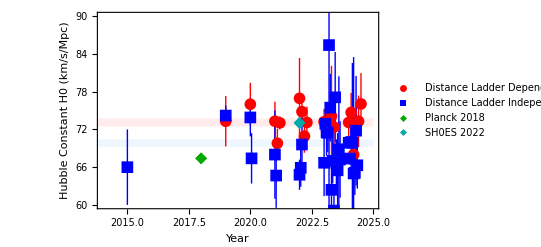

C:\Users\leand\Desktop\dl-tension\HubbleConstantPlot.pdf

```mathematica
(*Planck 2018 and SH0ES 2022 points*)
planck2018={2018,Around[67.4,0.5]};
sh0es2022={2022,Around[73.04,1.0]};

(*Create the plot using ListPlot*)
hubblePlot=ListPlot[{distanceLadderDependent,distanceLadderIndependent,{planck2018},{sh0es2022}},PlotStyle->{Red,Blue,{Darker[Green],PointSize[0.015]},{Darker[Cyan],PointSize[0.015]}},PlotMarkers->{{"●",12},{"■",12},{"◆",12},{"◆",12}},Frame->True,FrameLabel->{"Year","Hubble Constant H0 (km/s/Mpc)"},PlotRange->{{2014,2025},{60,90}},PlotLegends->{"Distance Ladder Dependent","Distance Ladder Independent","Planck 2018","SH0ES 2022"},IntervalMarkers->"Bars",IntervalMarkersStyle->{Red,Blue,Darker[Green],Darker[Cyan]},Joined->False,Prolog->{{Opacity[0.5,LightRed],Rectangle[{2010,73.1003-0.653403},{2025,73.1003+0.653403}]},{Opacity[0.5,LightBlue],Rectangle[{2010,69.8347-0.604},{2025,69.8347+0.604}]}}]

(*Export the plot to a PDF file*)
Export[FileNameJoin[{NotebookDirectory[],"HubbleConstantPlot.pdf"}],hubblePlot]
```

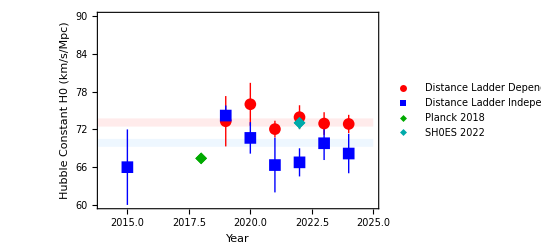

C:\Users\leand\Desktop\dl-tension\HubbleConstantPlotBinned.pdf

```mathematica
(*Function to merge points by year using the integer part of the year*)mergeDataByYear[data_List]:=Module[{grouped,averaged},(*Use Floor to take the integer part of the year before grouping*)grouped=GatherBy[data,Floor[#[[1]]]&];
averaged={#[[1,1]],Mean[#[[All,2]]]}&/@grouped;
Return[averaged];];

(*Merged data*)
mergedDistanceLadderDependent=mergeDataByYear[distanceLadderDependent];
mergedDistanceLadderIndependent=mergeDataByYear[distanceLadderIndependent];

(*Create the plot*)
hubblePlot=ListPlot[{mergedDistanceLadderDependent,mergedDistanceLadderIndependent,{planck2018},{sh0es2022}},PlotStyle->{Red,Blue,{Darker[Green],PointSize[0.015]},{Darker[Cyan],PointSize[0.015]}},PlotMarkers->{{"●",12},{"■",12},{"◆",12},{"◆",12}},Frame->True,FrameLabel->{"Year","Hubble Constant H0 (km/s/Mpc)"},PlotRange->{{2014,2025},{60,90}},PlotLegends->{"Distance Ladder Dependent","Distance Ladder Independent","Planck 2018","SH0ES 2022"},IntervalMarkers->"Bars",IntervalMarkersStyle->{Red,Blue,Darker[Green],Darker[Cyan]},Joined->False,Prolog->{{Opacity[0.5,LightRed],Rectangle[{2010,73.1003-0.653403},{2025,73.1003+0.653403}]},{Opacity[0.5,LightBlue],Rectangle[{2010,69.8347-0.604},{2025,69.8845+0.604}]}}]

(*Export the plot to a PDF file*)
Export[FileNameJoin[{NotebookDirectory[],"HubbleConstantPlotBinned.pdf"}],hubblePlot]
```

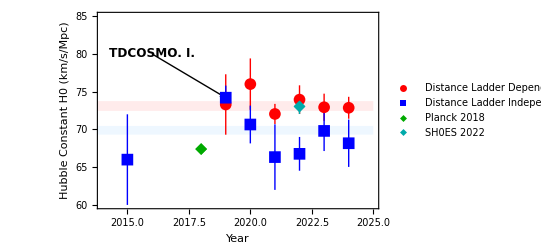

C:\Users\leand\Desktop\dl-tension\HubbleConstantBinnedPlot.pdf

```mathematica
(*Create the plot with specified adjustments*)hubblePlot=ListPlot[{mergedDistanceLadderDependent,mergedDistanceLadderIndependent,{planck2018},{sh0es2022}},PlotStyle->{Red,Blue,{Darker[Green],PointSize[0.015]},{Darker[Cyan],PointSize[0.015]}},PlotMarkers->{{"●",12},{"■",12},{"◆",12},{"◆",12}},Frame->True,FrameLabel->{"Year","Hubble Constant H0 (km/s/Mpc)"},PlotRange->{{2014,2025},{60,85}},(*Adjusted vertical range*)PlotLegends->{"Distance Ladder Dependent","Distance Ladder Independent","Planck 2018","SH0ES 2022"},IntervalMarkers->"Bars",IntervalMarkersStyle->{Red,Blue,Darker[Green],Darker[Cyan]},Joined->False,Prolog->{{Opacity[0.5,LightRed],Rectangle[{2010,73.1003-0.653403},{2025,73.1003+0.653403}]},{Opacity[0.5,LightBlue],Rectangle[{2010,69.8845-0.572741},{2025,69.8845+0.572741}]}},Epilog->{{Arrowheads[0.02],Arrow[{{2016,80},{2019,74.2}}]},(*Adjust the arrow to point from the new text position to the blue point of 2019*)Text[Style["TDCOSMO. I.","Times",Bold,12],{2016,80}]  (*Center the text at (2016,80) using Times font*)}]
Export[FileNameJoin[{NotebookDirectory[],"HubbleConstantBinnedPlot.pdf"}],hubblePlot]
```

```mathematica
(*Define the H0 measurements and their errors*)hubbleData={{59,3,11},(*{H0,statistical error,systematic error}*){75,7,0},(*Assuming no systematic error reported*){71,12,0},(*Assuming no systematic error reported*){75.8,5.2,2.8},{75.4,3.8,1.5}};

(*Calculate total errors by adding statistical and systematic errors in quadrature*)
totalErrors=Sqrt[#2^2+#3^2]&@@@hubbleData;

(*Calculate weights for each measurement (inverse of the square of total error)*)
weights=1/totalErrors^2;

(*Calculate the weighted mean of H0*)
weightedMeanH0=Total[(#[[1]]*weights[[#2]])&@@@Thread[{hubbleData,Range[Length[hubbleData]]}]]/Total[weights];

(*Calculate the mean uncertainty as the mean of the total errors*)
meanUncertainty=Mean[totalErrors];

(*Output the results*)
{weightedMeanH0,meanUncertainty}
```

{74.1592,8.0786}

```mathematica
Length[distanceLadderIndependent]
```

33

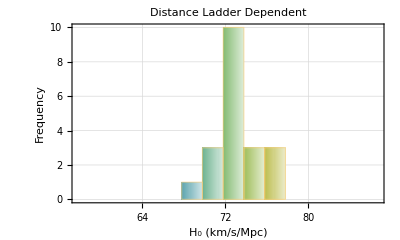

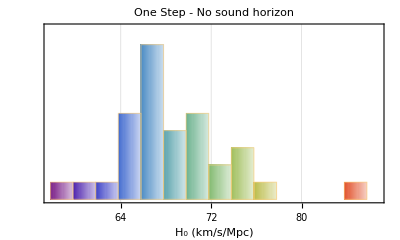

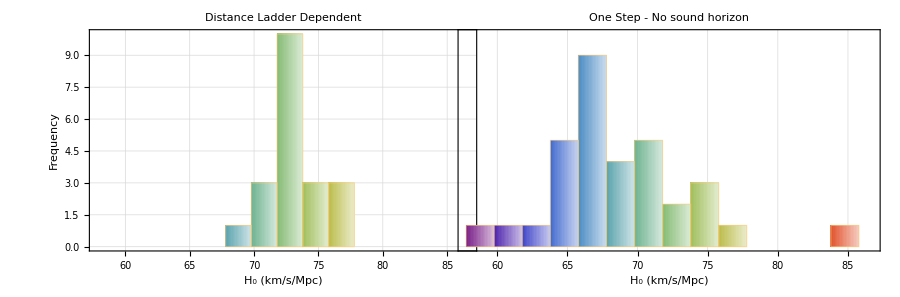

C:\Users\leand\Desktop\dl-tension\H0_Comparison.pdf

```mathematica
data1=distanceLadderDependent[[All,2]];
values1=N[data1[[All,1]]];

data2=distanceLadderIndependent[[All,2]];
values2=N[data2[[All,1]]];

minH0=Min[Min[values1],Min[values2]];
maxH0=Max[Max[values1],Max[values2]];

padding=(maxH0-minH0)*0.05;
plotRange={minH0-padding,maxH0+padding};

binWidth=2;
bins=Range[plotRange[[1]],plotRange[[2]],binWidth];

maxFreq=Max[HistogramList[values1,{bins}][[2]],HistogramList[values2,{bins}][[2]]];

colorFunction=ColorData["Rainbow"];
binColors=Table[colorFunction[x],{x,0,1,1/(Length[bins]-1)}];

histogramSettings={PlotRange->{{plotRange[[1]],plotRange[[2]]},{0,maxFreq}},Frame->True,FrameStyle->Directive[Black,12],PlotTheme->"Detailed",ChartStyle->binColors,ChartElementFunction->"FadingRectangle",ImageSize->400,AspectRatio->0.6};

pl1=Histogram[values1,{bins},PlotLabel->"Distance Ladder Dependent",FrameLabel->{{"Frequency",None},{Subscript["H",0] " (km/s/Mpc)",None}},Evaluate[histogramSettings]]

pl2=Histogram[values2,{bins},PlotLabel->"One Step - No sound horizon",FrameLabel->{{None,None},{Subscript["H",0] " (km/s/Mpc)",None}},FrameTicks->{{None,None},{Automatic,None}},Evaluate[histogramSettings]]

colorLegend=BarLegend[{"Rainbow",{minH0,maxH0}},LegendLabel->Subscript["H",0] " (km/s/Mpc)"];

combinedPlot=GraphicsRow[{pl1,pl2},Spacings->-75];

finalPlot=Legended[combinedPlot,Placed[colorLegend,Right]];

finalImage=Show[finalPlot,PlotRange->All,ImageSize->900,PlotLabel->Style["Comparison of "Subscript["H",0]" Measurements",16,Bold]]

(*Export the plot as a PDF file*)
Export[FileNameJoin[{NotebookDirectory[],"H0_Comparison.pdf"}],finalImage]
```

Kolmogorov-Smirnov Test Results:

p-value: 0.0000266381

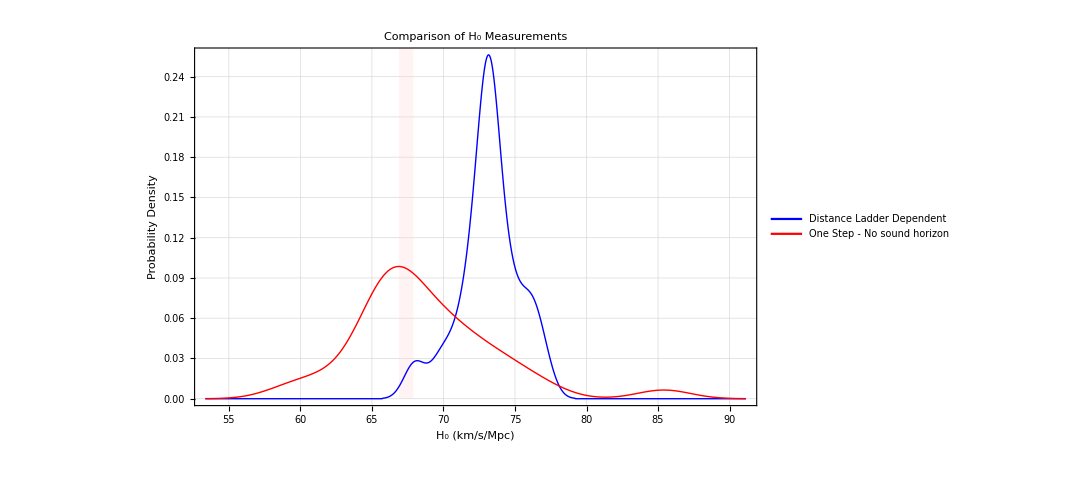

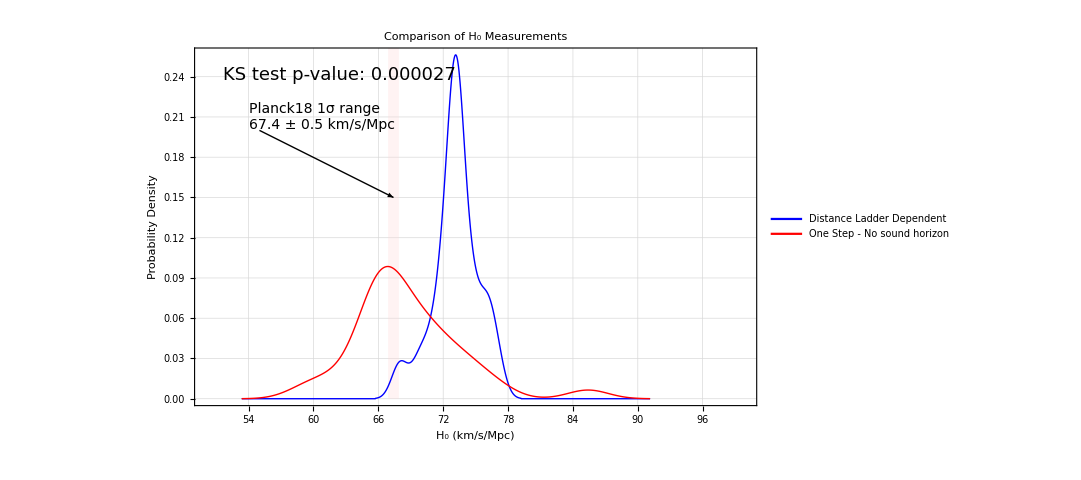

C:\Users\leand\Desktop\dl-tension\H0_SmoothHistogram_Comparison.pdf

```mathematica
dependent=N[distanceLadderDependent[[All,2,1]]];
independent=N[distanceLadderIndependent[[All,2,1]]];

ksTest=KolmogorovSmirnovTest[dependent,independent];

Print["Kolmogorov-Smirnov Test Results:"]
Print["p-value: ",ksTest]

(*Define Planck18 H₀ value and uncertainty*)
planckH0=67.4;(*Planck18 H₀ value*)planckUncertainty=0.5;(*Planck18 1σ uncertainty*)(*Create the vertical band*)planckBand=Rectangle[{planckH0-planckUncertainty,0},{planckH0+planckUncertainty,1}];

plot=SmoothHistogram[{dependent,independent},PlotRange->All,Frame->True,FrameLabel->{Style[Subscript["H",0] " (km/s/Mpc)",16],Style["Probability Density",16]},PlotLabel->Style["Comparison of "Subscript["H",0]" Measurements",16,Bold],PlotStyle->{{Thick,Blue},{Thick,Red}},PlotLegends->Placed[LineLegend[{Style["Distance Ladder Dependent",16],Style["One Step - No sound horizon",16]},LegendFunction->Frame],{0.75,0.8}],ImageSize->800,AspectRatio->0.6,BaseStyle->{FontFamily->"Times",FontSize->16},AxesStyle->Directive[Black,16],FrameStyle->Directive[Black,16],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],Prolog->{Opacity[0.3],LightRed,planckBand}]

(*Add KS test result to the plot*)
ksAnnotation=Text[Style["KS test p-value: "<>ToString[NumberForm[ksTest,{7,6}]],18],Scaled[{0.05,0.95}],{-1,1}];

(*Create arrow and label for Planck18 band*)
planckArrow=Arrow[{{55,0.2},{planckH0,0.15}}];
planckLabel=Text[Style["Planck18 1σ range\n"<>ToString[planckH0]<>" ± "<>ToString[planckUncertainty]<>" km/s/Mpc",14],{54,0.21},{-1,0}];

(*Combine everything*)
finalPlot=Show[plot,Epilog->{ksAnnotation,planckArrow,planckLabel},PlotRange->{{50,100},All}  (*Adjust x-range as needed*)]

(*Export the plot as a PDF file*)
Export[FileNameJoin[{NotebookDirectory[],"H0_SmoothHistogram_Comparison.pdf"}],finalPlot]
```

## Full Datasets (Indexed)

```mathematica
(*Data for distance ladder dependent measurements*)distanceLadderDependent={{1,Around[73.3,4.0]},{2,Around[76.0,3.4]},{3,Around[73.3,3.1]},{4,Around[69.8,2.3]},{5,Around[73.04,1.04]},{6,Around[76.94,6.4]},{7,Around[74.82,1.81]},{8,Around[70.92,2.63]},{9,Around[73.1,2.5]},{10,Around[73.22,2.06]},{11,Around[71.76,1.32]},{12,Around[73.22,1.45]},{13,Around[74.1,8.0]},{14,Around[72.37,2.97]},{15,Around[73.1,2.3]},{16,Around[74.7,3.1]},{17,Around[68.00,2.7]},{18,Around[72.05,3.6]},{19,Around[73.3,4.08]},{20,Around[76.05,4.90]}};

distanceLadderIndependent={{1,Around[61,18]},{2,Around[68,9]},{3,Around[66.0,6.0]},{4,Around[74.2,1.6]},{5,Around[73.9,3.0]},{6,Around[67.4,4]},{7,Around[68.0,7]},{8,Around[64.67,5.14]},{9,Around[64.8,2.4]},{10,Around[65.9,3.0]},{11,Around[69.6,5.5]},{12,Around[66.7,5.3]},{13,Around[72.9,2.15]},{14,Around[71.5,3.7]},{15,Around[71.5,3.1]},{16,Around[85.4,31.5]},{17,Around[75.46,5.365]},{18,Around[62.4,4.0]},{19,Around[67.0,3.6]},{20,Around[59.1,3.55]},{21,Around[77.1,7.2]},{22,Around[66.6,3.8]},{23,Around[65.5,5.9]},{24,Around[68.84,11.6]},{25,Around[67.22,6.07]},{26,Around[69.88,0.93]},{27,Around[67.37,0.96]},{28,Around[70.0,4.8]},{29,Around[69.9,12.65]},{30,Around[65,18.5]},{31,Around[65.1,3.5]},{32,Around[71.8,8.7]},{33,Around[66.3,3.7]}};

(*Function to calculate weighted mean and standard deviation*)
calculateWeightedMean[data_]:=Module[{h0Values,uncertainties,weights,weightedH0,weightedMeanH0,stdDeviation},h0Values=data[[All,2]]/. Around[value_,_]:>value;
uncertainties=data[[All,2]]/. Around[_,error_]:>error;
(*Calculate weights based on the uncertainties*)weights=1/(uncertainties^2);
(*Calculate weighted H0*)weightedH0=(h0Values*weights)/Total[weights];
(*Calculate the weighted mean of H0*)weightedMeanH0=Total[weightedH0];
(*Calculate the standard deviation of the weighted mean*)stdDeviation=Sqrt[1/Total[weights]];
(*Output the results*)<|"Weighted Mean H0"->weightedMeanH0,"Standard Deviation"->stdDeviation|>]

(*Calculate results for both datasets*)
resultsDependent=calculateWeightedMean[distanceLadderDependent];
resultsIndependent=calculateWeightedMean[distanceLadderIndependent];

(*Output the results*)
<|"Distance Ladder Dependent"->resultsDependent,"Distance Ladder Independent"->resultsIndependent|>
```

<|Distance Ladder Dependent→<|Weighted Mean H0→72.7716,Standard Deviation→0.498493|>,Distance Ladder Independent→<|Weighted Mean H0→68.9668,Standard Deviation→0.48332|>|>

## χ2 Calculations

### Full Data

Distance Ladder Dependent Dataset Analysis:

Best fit H0: 72.80.50.5

Minimum χ.b2: 9.7132

Reduced χ.b2: 0.511221

Degrees of freedom: 19

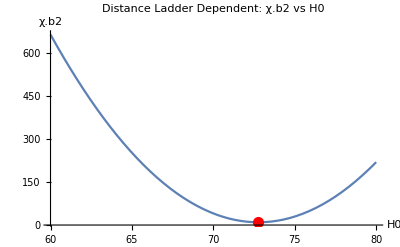

Distance Ladder Independent Dataset Analysis:

Best fit H0: 69.00.50.5

Minimum χ.b2: 43.6863

Reduced χ.b2: 1.3652

Degrees of freedom: 32

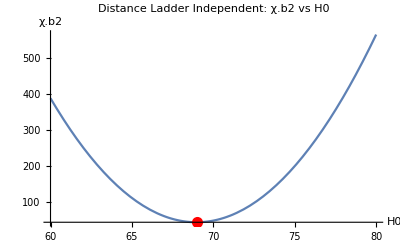

```mathematica
(*Define the chi-square function*)
chiSquare[h0_,data_]:=Sum[((h0-data[[i,2]][[1]])/data[[i,2]][[2]])^2,{i,1,Length[data]}]

(*Function to perform analysis on a dataset*)analyzeDataset[data_,name_]:=Module[{minChiSquare,bestH0,dof,reducedChiSquare,h0Lower,h0Upper},{minChiSquare,bestH0Rule}=NMinimize[{chiSquare[h0,data],60<=h0<=80},h0];
bestH0=bestH0Rule[[1,2]];(*Use Part to extract the numerical value*)dof=Length[data]-1;
reducedChiSquare=minChiSquare/dof;
deltaChiSquare[h0_]:=chiSquare[h0,data]-minChiSquare;
h0Lower=FindRoot[deltaChiSquare[h0]==1,{h0,bestH0-1}][[1,2]];
h0Upper=FindRoot[deltaChiSquare[h0]==1,{h0,bestH0+1}][[1,2]];
Print[Style[name<>" Dataset Analysis:",Bold,Larger]];
Print["Best fit H0: ",Around[bestH0,{bestH0-h0Lower,h0Upper-bestH0}]];
Print["Minimum χ.b2: ",minChiSquare];
Print["Reduced χ.b2: ",reducedChiSquare];
Print["Degrees of freedom: ",dof];
Print[];
Show[Plot[chiSquare[h0,data],{h0,60,80},PlotLabel->name<>": χ.b2 vs H0",AxesLabel->{"H0","χ.b2"},PlotRange->All],Graphics[{Red,PointSize[0.02],Point[{bestH0,minChiSquare}]}]]]
(*Analyze Distance Ladder Dependent Dataset*)analyzeDataset[distanceLadderDependent,"Distance Ladder Dependent"]

(*Analyze Distance Ladder Independent Dataset*)
analyzeDataset[distanceLadderIndependent,"Distance Ladder Independent"]
```

### Exclude points 4 and 5 (TDCOSMO I and Megamasers SH0ES)

Full Distance Ladder Dependent Dataset Analysis:

Excluded data points: {}

Number of data points used: 20

Best fit H0: 72.80.50.5

Minimum χ.b2.b2: 9.7132

Reduced χ.b2.b2: 0.511221

Degrees of freedom: 19

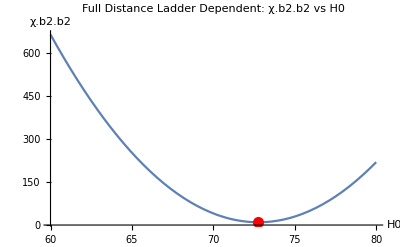

Distance Ladder Independent (excluding points outlier points 4 and 5 (TDCOSMO.I and MCP SH0ES)) Dataset Analysis:

Excluded data points: {4,5}

Number of data points used: 31

Best fit H0: 68.30.50.5

Minimum χ.b2.b2: 28.5062

Reduced χ.b2.b2: 0.950208

Degrees of freedom: 30

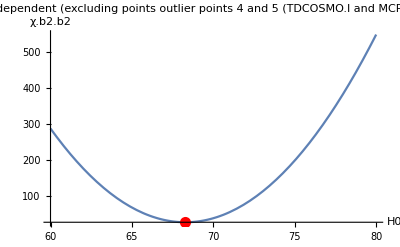

```mathematica
(*Define the chi-square function*)
chiSquare[h0_,data_]:=Sum[((h0-data[[i,2]][[1]])/data[[i,2]][[2]])^2,{i,1,Length[data]}]

(*Function to perform analysis on a dataset*)
analyzeDataset[fullData_,excludeIndices_,name_]:=Module[{data,minChiSquare,bestH0,dof,reducedChiSquare,h0Lower,h0Upper},(*Remove the specified data points*)data=Delete[fullData,List/@excludeIndices];
{minChiSquare,bestH0Rule}=NMinimize[{chiSquare[h0,data],60<=h0<=80},h0];
bestH0=bestH0Rule[[1,2]];(*Use Part to extract the numerical value*)dof=Length[data]-1;
reducedChiSquare=minChiSquare/dof;
deltaChiSquare[h0_]:=chiSquare[h0,data]-minChiSquare;
h0Lower=FindRoot[deltaChiSquare[h0]==1,{h0,bestH0-1}][[1,2]];
h0Upper=FindRoot[deltaChiSquare[h0]==1,{h0,bestH0+1}][[1,2]];
Print[Style[name<>" Dataset Analysis:",Bold,Larger]];
Print["Excluded data points: ",excludeIndices];
Print["Number of data points used: ",Length[data]];
Print["Best fit H0: ",Around[bestH0,{bestH0-h0Lower,h0Upper-bestH0}]];
Print["Minimum χ.b2.b2: ",minChiSquare];
Print["Reduced χ.b2.b2: ",reducedChiSquare];
Print["Degrees of freedom: ",dof];
Print[];
Show[Plot[chiSquare[h0,data],{h0,60,80},PlotLabel->name<>": χ.b2.b2 vs H0",AxesLabel->{"H0","χ.b2.b2"},PlotRange->All],Graphics[{Red,PointSize[0.02],Point[{bestH0,minChiSquare}]}]]]

(*Example usage*)
(*Analyze full Distance Ladder Dependent Dataset*)
analyzeDataset[distanceLadderDependent,{},"Full Distance Ladder Dependent"]

(*Analyze Distance Ladder Independent Dataset excluding points 4 and 5*)
analyzeDataset[distanceLadderIndependent,{4,5},"Distance Ladder Independent (excluding points outlier points 4 and 5 (TDCOSMO.I and MCP SH0ES))"]
```

### Subset GW

Full Distance Ladder Dependent Dataset Analysis:

Data points used: {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

Best fit H0: 72.80.50.5

Minimum χ.b2.b2: 9.7132

Reduced χ.b2.b2: 0.511221

Degrees of freedom: 19

-Graphics-

Subset of Distance Ladder Independent using GW Dataset Analysis:

Data points used: {7,11,16,17,24,29}

Best fit H0: 71.43.13.1

Minimum χ.b2.b2: 1.17596

Reduced χ.b2.b2: 0.235192

Degrees of freedom: 5

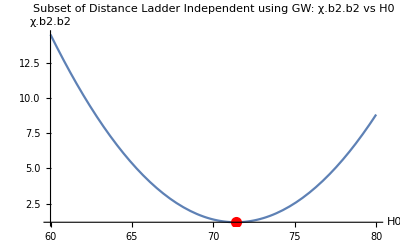

Data points used: {7,11,16,17,24}

Best fit H0: 71.53.23.2

Minimum χ.b2.b2: 1.1614

Reduced χ.b2.b2: 0.290349

Degrees of freedom: 4

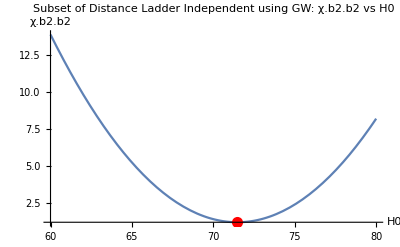

```mathematica
(*Define the chi-square function*)
chiSquare[h0_,data_]:=Sum[((h0-data[[i,2]][[1]])/data[[i,2]][[2]])^2,{i,1,Length[data]}]

(*Function to perform analysis on a dataset*)
analyzeDataset[fullData_,indices_,name_]:=Module[{data,minChiSquare,bestH0,dof,reducedChiSquare,h0Lower,h0Upper},(*Select the specified data points*)data=fullData[[indices]];
{minChiSquare,bestH0Rule}=NMinimize[{chiSquare[h0,data],60<=h0<=80},h0];
bestH0=bestH0Rule[[1,2]];(*Use Part to extract the numerical value*)dof=Length[data]-1;
reducedChiSquare=minChiSquare/dof;
deltaChiSquare[h0_]:=chiSquare[h0,data]-minChiSquare;
h0Lower=FindRoot[deltaChiSquare[h0]==1,{h0,bestH0-1}][[1,2]];
h0Upper=FindRoot[deltaChiSquare[h0]==1,{h0,bestH0+1}][[1,2]];
Print[Style[name<>" Dataset Analysis:",Bold,Larger]];
Print["Data points used: ",indices];
Print["Best fit H0: ",Around[bestH0,{bestH0-h0Lower,h0Upper-bestH0}]];
Print["Minimum χ.b2.b2: ",minChiSquare];
Print["Reduced χ.b2.b2: ",reducedChiSquare];
Print["Degrees of freedom: ",dof];
Print[];
Show[Plot[chiSquare[h0,data],{h0,60,80},PlotLabel->name<>": χ.b2.b2 vs H0",AxesLabel->{"H0","χ.b2.b2"},PlotRange->All],Graphics[{Red,PointSize[0.02],Point[{bestH0,minChiSquare}]}]]]

(*Example usage*)
(*Analyze full Distance Ladder Dependent Dataset*)
analyzeDataset[distanceLadderDependent,Range[Length[distanceLadderDependent]],"Full Distance Ladder Dependent"]

(*Analyze subset of Distance Ladder Independent Dataset*)
analyzeDataset[distanceLadderIndependent,{7,11,16,17,24,29},"Subset of Distance Ladder Independent using GW"]
```

### Subset All - Exclude GW

Full Distance Ladder Dependent Dataset Analysis:

Excluded data points: {}

Number of data points used: 20

Best fit H0: 72.80.50.5

Minimum χ.b2.b2: 9.7132

Reduced χ.b2.b2: 0.511221

Degrees of freedom: 19

-Graphics-

Distance Ladder Independent (excluding points GW: {7,11,16,17,24,29}) Dataset Analysis:

Excluded data points: {7,11,16,17,24,29,4,5}

Number of data points used: 25

Best fit H0: 68.20.50.5

Minimum χ.b2.b2: 26.3148

Reduced χ.b2.b2: 1.09645

Degrees of freedom: 24

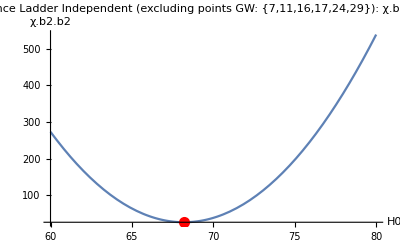

```mathematica
(*Define the chi-square function*)
chiSquare[h0_,data_]:=Sum[((h0-data[[i,2]][[1]])/data[[i,2]][[2]])^2,{i,1,Length[data]}]

(*Function to perform analysis on a dataset*)
analyzeDataset[fullData_,excludeIndices_,name_]:=Module[{data,minChiSquare,bestH0,dof,reducedChiSquare,h0Lower,h0Upper},(*Remove the specified data points*)data=Delete[fullData,List/@excludeIndices];
{minChiSquare,bestH0Rule}=NMinimize[{chiSquare[h0,data],60<=h0<=80},h0];
bestH0=bestH0Rule[[1,2]];(*Use Part to extract the numerical value*)dof=Length[data]-1;
reducedChiSquare=minChiSquare/dof;
deltaChiSquare[h0_]:=chiSquare[h0,data]-minChiSquare;
h0Lower=FindRoot[deltaChiSquare[h0]==1,{h0,bestH0-1}][[1,2]];
h0Upper=FindRoot[deltaChiSquare[h0]==1,{h0,bestH0+1}][[1,2]];
Print[Style[name<>" Dataset Analysis:",Bold,Larger]];
Print["Excluded data points: ",excludeIndices];
Print["Number of data points used: ",Length[data]];
Print["Best fit H0: ",Around[bestH0,{bestH0-h0Lower,h0Upper-bestH0}]];
Print["Minimum χ.b2.b2: ",minChiSquare];
Print["Reduced χ.b2.b2: ",reducedChiSquare];
Print["Degrees of freedom: ",dof];
Print[];
Show[Plot[chiSquare[h0,data],{h0,60,80},PlotLabel->name<>": χ.b2.b2 vs H0",AxesLabel->{"H0","χ.b2.b2"},PlotRange->All],Graphics[{Red,PointSize[0.02],Point[{bestH0,minChiSquare}]}]]]

(*Example usage*)
(*Analyze full Distance Ladder Dependent Dataset*)
analyzeDataset[distanceLadderDependent,{},"Full Distance Ladder Dependent"]

(*Analyze Distance Ladder Independent Dataset excluding points 4 and 5*)
analyzeDataset[distanceLadderIndependent,{7,11,16,17,24,29,4,5},"Distance Ladder Independent (excluding points GW: {7,11,16,17,24,29})"]
```

### Subset Lensing All

Full Distance Ladder Dependent Dataset Analysis:

Data points used: {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

Best fit H0: 72.80.50.5

Minimum χ.b2.b2: 9.7132

Reduced χ.b2.b2: 0.511221

Degrees of freedom: 19

-Graphics-

Subset of Distance Ladder Independent Using Time Delay and Strong Lensing Dataset Analysis:

Data points used: {4,6,13,14,21,22,28,31,32,33}

Best fit H0: 71.41.01.0

Minimum χ.b2.b2: 11.9993

Reduced χ.b2.b2: 1.33325

Degrees of freedom: 9

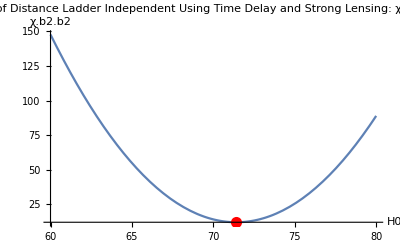

```mathematica
(*Define the chi-square function*)
chiSquare[h0_,data_]:=Sum[((h0-data[[i,2]][[1]])/data[[i,2]][[2]])^2,{i,1,Length[data]}]

(*Function to perform analysis on a dataset*)
analyzeDataset[fullData_,indices_,name_]:=Module[{data,minChiSquare,bestH0,dof,reducedChiSquare,h0Lower,h0Upper},(*Select the specified data points*)data=fullData[[indices]];
{minChiSquare,bestH0Rule}=NMinimize[{chiSquare[h0,data],60<=h0<=80},h0];
bestH0=bestH0Rule[[1,2]];(*Use Part to extract the numerical value*)dof=Length[data]-1;
reducedChiSquare=minChiSquare/dof;
deltaChiSquare[h0_]:=chiSquare[h0,data]-minChiSquare;
h0Lower=FindRoot[deltaChiSquare[h0]==1,{h0,bestH0-1}][[1,2]];
h0Upper=FindRoot[deltaChiSquare[h0]==1,{h0,bestH0+1}][[1,2]];
Print[Style[name<>" Dataset Analysis:",Bold,Larger]];
Print["Data points used: ",indices];
Print["Best fit H0: ",Around[bestH0,{bestH0-h0Lower,h0Upper-bestH0}]];
Print["Minimum χ.b2.b2: ",minChiSquare];
Print["Reduced χ.b2.b2: ",reducedChiSquare];
Print["Degrees of freedom: ",dof];
Print[];
Show[Plot[chiSquare[h0,data],{h0,60,80},PlotLabel->name<>": χ.b2.b2 vs H0",AxesLabel->{"H0","χ.b2.b2"},PlotRange->All],Graphics[{Red,PointSize[0.02],Point[{bestH0,minChiSquare}]}]]]

(*Analyze full Distance Ladder Dependent Dataset*)
analyzeDataset[distanceLadderDependent,Range[Length[distanceLadderDependent]],"Full Distance Ladder Dependent"]

(*Analyze subset of Distance Ladder Independent Dataset*)
analyzeDataset[distanceLadderIndependent,{4,6,13,14,21,22,28,31,32,33},"Subset of Distance Ladder Independent Using Time Delay and Strong Lensing"]
```

### Subset All - Exclude All Lensing

Full Distance Ladder Dependent Dataset Analysis:

Excluded data points: {}

Number of data points used: 20

Best fit H0: 72.80.50.5

Minimum χ.b2.b2: 9.7132

Reduced χ.b2.b2: 0.511221

Degrees of freedom: 19

-Graphics-

Distance Ladder Independent (excluding points Lensing: {4,6,13,14,21,22,28,31,32,33,5}) Dataset Analysis:

Excluded data points: {4,6,13,14,21,22,28,31,32,33}

Number of data points used: 23

Best fit H0: 68.20.60.6

Minimum χ.b2.b2: 23.4601

Reduced χ.b2.b2: 1.06637

Degrees of freedom: 22

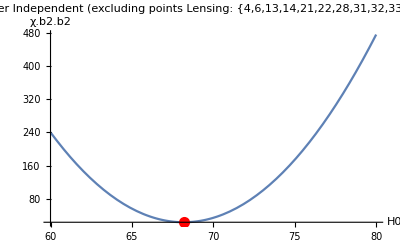

```mathematica
(*Define the chi-square function*)
chiSquare[h0_,data_]:=Sum[((h0-data[[i,2]][[1]])/data[[i,2]][[2]])^2,{i,1,Length[data]}]

(*Function to perform analysis on a dataset*)
analyzeDataset[fullData_,excludeIndices_,name_]:=Module[{data,minChiSquare,bestH0,dof,reducedChiSquare,h0Lower,h0Upper},(*Remove the specified data points*)data=Delete[fullData,List/@excludeIndices];
{minChiSquare,bestH0Rule}=NMinimize[{chiSquare[h0,data],60<=h0<=80},h0];
bestH0=bestH0Rule[[1,2]];(*Use Part to extract the numerical value*)dof=Length[data]-1;
reducedChiSquare=minChiSquare/dof;
deltaChiSquare[h0_]:=chiSquare[h0,data]-minChiSquare;
h0Lower=FindRoot[deltaChiSquare[h0]==1,{h0,bestH0-1}][[1,2]];
h0Upper=FindRoot[deltaChiSquare[h0]==1,{h0,bestH0+1}][[1,2]];
Print[Style[name<>" Dataset Analysis:",Bold,Larger]];
Print["Excluded data points: ",excludeIndices];
Print["Number of data points used: ",Length[data]];
Print["Best fit H0: ",Around[bestH0,{bestH0-h0Lower,h0Upper-bestH0}]];
Print["Minimum χ.b2.b2: ",minChiSquare];
Print["Reduced χ.b2.b2: ",reducedChiSquare];
Print["Degrees of freedom: ",dof];
Print[];
Show[Plot[chiSquare[h0,data],{h0,60,80},PlotLabel->name<>": χ.b2.b2 vs H0",AxesLabel->{"H0","χ.b2.b2"},PlotRange->All],Graphics[{Red,PointSize[0.02],Point[{bestH0,minChiSquare}]}]]]

(*Example usage*)
(*Analyze full Distance Ladder Dependent Dataset*)
analyzeDataset[distanceLadderDependent,{},"Full Distance Ladder Dependent"]

(*Analyze Distance Ladder Independent Dataset excluding points related to lensing ie {4,6,13,14,21,22,28,31,32,33}*)
analyzeDataset[distanceLadderIndependent,{4,6,13,14,21,22,28,31,32,33},"Distance Ladder Independent (excluding points Lensing: {4,6,13,14,21,22,28,31,32,33,5})"]
```

### Subset Lensing (no TDCOSMO I)

Full Distance Ladder Dependent Dataset Analysis:

Data points used: {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

Best fit H0: 72.80.50.5

Minimum χ.b2.b2: 9.7132

Reduced χ.b2.b2: 0.511221

Degrees of freedom: 19

-Graphics-

Subset of Distance Ladder Independent Including Lensing only without TDCOSO.I Dataset Analysis:

Data points used: {6,13,14,21,22,28,31,32,33}

Best fit H0: 69.71.21.2

Minimum χ.b2.b2: 7.13736

Reduced χ.b2.b2: 0.89217

Degrees of freedom: 8

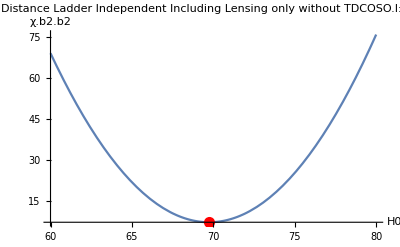

```mathematica
(*Define the chi-square function*)
chiSquare[h0_,data_]:=Sum[((h0-data[[i,2]][[1]])/data[[i,2]][[2]])^2,{i,1,Length[data]}]

(*Function to perform analysis on a dataset*)
analyzeDataset[fullData_,indices_,name_]:=Module[{data,minChiSquare,bestH0,dof,reducedChiSquare,h0Lower,h0Upper},(*Select the specified data points*)data=fullData[[indices]];
{minChiSquare,bestH0Rule}=NMinimize[{chiSquare[h0,data],60<=h0<=80},h0];
bestH0=bestH0Rule[[1,2]];(*Use Part to extract the numerical value*)dof=Length[data]-1;
reducedChiSquare=minChiSquare/dof;
deltaChiSquare[h0_]:=chiSquare[h0,data]-minChiSquare;
h0Lower=FindRoot[deltaChiSquare[h0]==1,{h0,bestH0-1}][[1,2]];
h0Upper=FindRoot[deltaChiSquare[h0]==1,{h0,bestH0+1}][[1,2]];
Print[Style[name<>" Dataset Analysis:",Bold,Larger]];
Print["Data points used: ",indices];
Print["Best fit H0: ",Around[bestH0,{bestH0-h0Lower,h0Upper-bestH0}]];
Print["Minimum χ.b2.b2: ",minChiSquare];
Print["Reduced χ.b2.b2: ",reducedChiSquare];
Print["Degrees of freedom: ",dof];
Print[];
Show[Plot[chiSquare[h0,data],{h0,60,80},PlotLabel->name<>": χ.b2.b2 vs H0",AxesLabel->{"H0","χ.b2.b2"},PlotRange->All],Graphics[{Red,PointSize[0.02],Point[{bestH0,minChiSquare}]}]]]

(*Analyze full Distance Ladder Dependent Dataset*)
analyzeDataset[distanceLadderDependent,Range[Length[distanceLadderDependent]],"Full Distance Ladder Dependent"]

(*Analyze subset of Distance Ladder Independent Dataset*)
analyzeDataset[distanceLadderIndependent,{6,13,14,21,22,28,31,32,33},"Subset of Distance Ladder Independent Including Lensing only without TDCOSO.I"]
```

### Subset Cosmic Chronometers

Full Distance Ladder Dependent Dataset Analysis:

Data points used: {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

Best fit H0: 72.80.50.5

Minimum χ.b2.b2: 9.7132

Reduced χ.b2.b2: 0.511221

Degrees of freedom: 19

-Graphics-

Subset of Distance Ladder Independent Including only Cosmic Chronometers Dataset Analysis:

Data points used: {10,12,15}

Best fit H0: 68.32.02.0

Minimum χ.b2.b2: 1.79634

Reduced χ.b2.b2: 0.898171

Degrees of freedom: 2

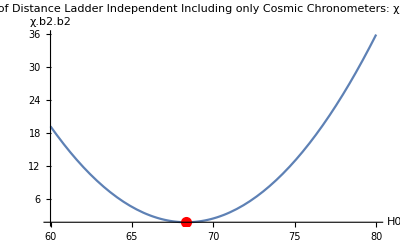

```mathematica
(*Define the chi-square function*)
chiSquare[h0_,data_]:=Sum[((h0-data[[i,2]][[1]])/data[[i,2]][[2]])^2,{i,1,Length[data]}]

(*Function to perform analysis on a dataset*)
analyzeDataset[fullData_,indices_,name_]:=Module[{data,minChiSquare,bestH0,dof,reducedChiSquare,h0Lower,h0Upper},(*Select the specified data points*)data=fullData[[indices]];
{minChiSquare,bestH0Rule}=NMinimize[{chiSquare[h0,data],60<=h0<=80},h0];
bestH0=bestH0Rule[[1,2]];(*Use Part to extract the numerical value*)dof=Length[data]-1;
reducedChiSquare=minChiSquare/dof;
deltaChiSquare[h0_]:=chiSquare[h0,data]-minChiSquare;
h0Lower=FindRoot[deltaChiSquare[h0]==1,{h0,bestH0-1}][[1,2]];
h0Upper=FindRoot[deltaChiSquare[h0]==1,{h0,bestH0+1}][[1,2]];
Print[Style[name<>" Dataset Analysis:",Bold,Larger]];
Print["Data points used: ",indices];
Print["Best fit H0: ",Around[bestH0,{bestH0-h0Lower,h0Upper-bestH0}]];
Print["Minimum χ.b2.b2: ",minChiSquare];
Print["Reduced χ.b2.b2: ",reducedChiSquare];
Print["Degrees of freedom: ",dof];
Print[];
Show[Plot[chiSquare[h0,data],{h0,60,80},PlotLabel->name<>": χ.b2.b2 vs H0",AxesLabel->{"H0","χ.b2.b2"},PlotRange->All],Graphics[{Red,PointSize[0.02],Point[{bestH0,minChiSquare}]}]]]

(*Analyze full Distance Ladder Dependent Dataset*)
analyzeDataset[distanceLadderDependent,Range[Length[distanceLadderDependent]],"Full Distance Ladder Dependent"]

(*Analyze subset of Distance Ladder Independent Dataset*)
analyzeDataset[distanceLadderIndependent,{10,12,15},"Subset of Distance Ladder Independent Including only Cosmic Chronometers"]
```

### Subset All - Exclude Cosmic Chronometers

Full Distance Ladder Dependent Dataset Analysis:

Excluded data points: {}

Number of data points used: 20

Best fit H0: 72.80.50.5

Minimum χ.b2.b2: 9.7132

Reduced χ.b2.b2: 0.511221

Degrees of freedom: 19

-Graphics-

Distance Ladder Independent (excluding Cosmic Chronometers: {10,12,15}) Dataset Analysis:

Excluded data points: {10,12,15,4,5}

Number of data points used: 28

Best fit H0: 68.30.50.5

Minimum χ.b2.b2: 26.709

Reduced χ.b2.b2: 0.989223

Degrees of freedom: 27

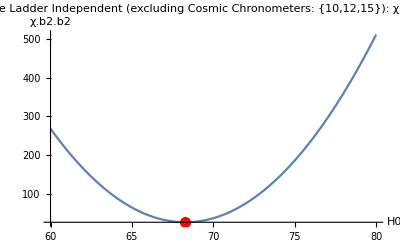

```mathematica
(*Define the chi-square function*)
chiSquare[h0_,data_]:=Sum[((h0-data[[i,2]][[1]])/data[[i,2]][[2]])^2,{i,1,Length[data]}]

(*Function to perform analysis on a dataset*)
analyzeDataset[fullData_,excludeIndices_,name_]:=Module[{data,minChiSquare,bestH0,dof,reducedChiSquare,h0Lower,h0Upper},(*Remove the specified data points*)data=Delete[fullData,List/@excludeIndices];
{minChiSquare,bestH0Rule}=NMinimize[{chiSquare[h0,data],60<=h0<=80},h0];
bestH0=bestH0Rule[[1,2]];(*Use Part to extract the numerical value*)dof=Length[data]-1;
reducedChiSquare=minChiSquare/dof;
deltaChiSquare[h0_]:=chiSquare[h0,data]-minChiSquare;
h0Lower=FindRoot[deltaChiSquare[h0]==1,{h0,bestH0-1}][[1,2]];
h0Upper=FindRoot[deltaChiSquare[h0]==1,{h0,bestH0+1}][[1,2]];
Print[Style[name<>" Dataset Analysis:",Bold,Larger]];
Print["Excluded data points: ",excludeIndices];
Print["Number of data points used: ",Length[data]];
Print["Best fit H0: ",Around[bestH0,{bestH0-h0Lower,h0Upper-bestH0}]];
Print["Minimum χ.b2.b2: ",minChiSquare];
Print["Reduced χ.b2.b2: ",reducedChiSquare];
Print["Degrees of freedom: ",dof];
Print[];
Show[Plot[chiSquare[h0,data],{h0,60,80},PlotLabel->name<>": χ.b2.b2 vs H0",AxesLabel->{"H0","χ.b2.b2"},PlotRange->All],Graphics[{Red,PointSize[0.02],Point[{bestH0,minChiSquare}]}]]]

(*Example usage*)
(*Analyze full Distance Ladder Dependent Dataset*)
analyzeDataset[distanceLadderDependent,{},"Full Distance Ladder Dependent"]

(*Analyze Distance Ladder Independent Dataset excluding Cosmic Chronometers points 10,12,15 *)
analyzeDataset[distanceLadderIndependent,{10,12,15,4,5},"Distance Ladder Independent (excluding Cosmic Chronometers: {10,12,15})"]
```

### Subset Megamasers

Full Distance Ladder Dependent Dataset Analysis:

Data points used: {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

Best fit H0: 72.80.50.5

Minimum χ.b2.b2: 9.7132

Reduced χ.b2.b2: 0.511221

Degrees of freedom: 19

-Graphics-

Subset of Distance Ladder Independent Including Only Megamasers Dataset Analysis:

Data points used: {2,3,5}

Best fit H0: 72.02.62.6

Minimum χ.b2.b2: 1.59848

Reduced χ.b2.b2: 0.79924

Degrees of freedom: 2

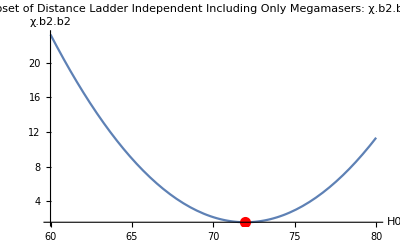

```mathematica
(*Define the chi-square function*)
chiSquare[h0_,data_]:=Sum[((h0-data[[i,2]][[1]])/data[[i,2]][[2]])^2,{i,1,Length[data]}]

(*Function to perform analysis on a dataset*)
analyzeDataset[fullData_,indices_,name_]:=Module[{data,minChiSquare,bestH0,dof,reducedChiSquare,h0Lower,h0Upper},(*Select the specified data points*)data=fullData[[indices]];
{minChiSquare,bestH0Rule}=NMinimize[{chiSquare[h0,data],60<=h0<=80},h0];
bestH0=bestH0Rule[[1,2]];(*Use Part to extract the numerical value*)dof=Length[data]-1;
reducedChiSquare=minChiSquare/dof;
deltaChiSquare[h0_]:=chiSquare[h0,data]-minChiSquare;
h0Lower=FindRoot[deltaChiSquare[h0]==1,{h0,bestH0-1}][[1,2]];
h0Upper=FindRoot[deltaChiSquare[h0]==1,{h0,bestH0+1}][[1,2]];
Print[Style[name<>" Dataset Analysis:",Bold,Larger]];
Print["Data points used: ",indices];
Print["Best fit H0: ",Around[bestH0,{bestH0-h0Lower,h0Upper-bestH0}]];
Print["Minimum χ.b2.b2: ",minChiSquare];
Print["Reduced χ.b2.b2: ",reducedChiSquare];
Print["Degrees of freedom: ",dof];
Print[];
Show[Plot[chiSquare[h0,data],{h0,60,80},PlotLabel->name<>": χ.b2.b2 vs H0",AxesLabel->{"H0","χ.b2.b2"},PlotRange->All],Graphics[{Red,PointSize[0.02],Point[{bestH0,minChiSquare}]}]]]

(*Analyze full Distance Ladder Dependent Dataset*)
analyzeDataset[distanceLadderDependent,Range[Length[distanceLadderDependent]],"Full Distance Ladder Dependent"]

(*Analyze subset of Distance Ladder Independent Dataset*)
analyzeDataset[distanceLadderIndependent,{2,3,5},"Subset of Distance Ladder Independent Including Only Megamasers"]
```

### Subset All - Exclude Megamasers

Full Distance Ladder Dependent Dataset Analysis:

Excluded data points: {}

Number of data points used: 20

Best fit H0: 72.80.50.5

Minimum χ.b2.b2: 9.7132

Reduced χ.b2.b2: 0.511221

Degrees of freedom: 19

-Graphics-

Distance Ladder Independent (excluding Megamasers: {2,3,5}) Dataset Analysis:

Excluded data points: {2,3,5,4}

Number of data points used: 29

Best fit H0: 68.30.50.5

Minimum χ.b2.b2: 28.3596

Reduced χ.b2.b2: 1.01284

Degrees of freedom: 28

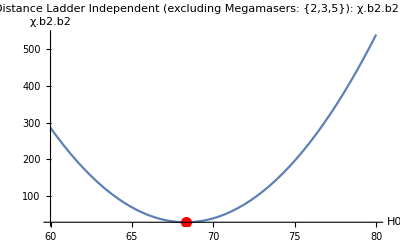

```mathematica
(*Define the chi-square function*)
chiSquare[h0_,data_]:=Sum[((h0-data[[i,2]][[1]])/data[[i,2]][[2]])^2,{i,1,Length[data]}]

(*Function to perform analysis on a dataset*)
analyzeDataset[fullData_,excludeIndices_,name_]:=Module[{data,minChiSquare,bestH0,dof,reducedChiSquare,h0Lower,h0Upper},(*Remove the specified data points*)data=Delete[fullData,List/@excludeIndices];
{minChiSquare,bestH0Rule}=NMinimize[{chiSquare[h0,data],60<=h0<=80},h0];
bestH0=bestH0Rule[[1,2]];(*Use Part to extract the numerical value*)dof=Length[data]-1;
reducedChiSquare=minChiSquare/dof;
deltaChiSquare[h0_]:=chiSquare[h0,data]-minChiSquare;
h0Lower=FindRoot[deltaChiSquare[h0]==1,{h0,bestH0-1}][[1,2]];
h0Upper=FindRoot[deltaChiSquare[h0]==1,{h0,bestH0+1}][[1,2]];
Print[Style[name<>" Dataset Analysis:",Bold,Larger]];
Print["Excluded data points: ",excludeIndices];
Print["Number of data points used: ",Length[data]];
Print["Best fit H0: ",Around[bestH0,{bestH0-h0Lower,h0Upper-bestH0}]];
Print["Minimum χ.b2.b2: ",minChiSquare];
Print["Reduced χ.b2.b2: ",reducedChiSquare];
Print["Degrees of freedom: ",dof];
Print[];
Show[Plot[chiSquare[h0,data],{h0,60,80},PlotLabel->name<>": χ.b2.b2 vs H0",AxesLabel->{"H0","χ.b2.b2"},PlotRange->All],Graphics[{Red,PointSize[0.02],Point[{bestH0,minChiSquare}]}]]]

(*Example usage*)
(*Analyze full Distance Ladder Dependent Dataset*)
analyzeDataset[distanceLadderDependent,{},"Full Distance Ladder Dependent"]

(*Analyze Distance Ladder Independent Dataset excluding Megamasers points 2,3,5 *)
analyzeDataset[distanceLadderIndependent,{2,3,5,4},"Distance Ladder Independent (excluding Megamasers: {2,3,5})"]
```

### Subset Megamasers no MCP+SH0ES

Full Distance Ladder Dependent Dataset Analysis:

Data points used: {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

Best fit H0: 72.80.50.5

Minimum χ.b2.b2: 9.7132

Reduced χ.b2.b2: 0.511221

Degrees of freedom: 19

-Graphics-

Subset of Distance Ladder Independent Including Only pure MCP Megamasers (no MCP-SH0ES) Dataset Analysis:

Data points used: {2,3}

Best fit H0: 67.5.5.

Minimum χ.b2.b2: 0.034188

Reduced χ.b2.b2: 0.034188

Degrees of freedom: 1

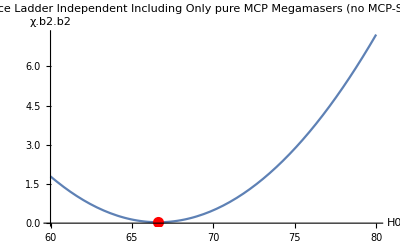

```mathematica
(*Define the chi-square function*)
chiSquare[h0_,data_]:=Sum[((h0-data[[i,2]][[1]])/data[[i,2]][[2]])^2,{i,1,Length[data]}]

(*Function to perform analysis on a dataset*)
analyzeDataset[fullData_,indices_,name_]:=Module[{data,minChiSquare,bestH0,dof,reducedChiSquare,h0Lower,h0Upper},(*Select the specified data points*)data=fullData[[indices]];
{minChiSquare,bestH0Rule}=NMinimize[{chiSquare[h0,data],60<=h0<=80},h0];
bestH0=bestH0Rule[[1,2]];(*Use Part to extract the numerical value*)dof=Length[data]-1;
reducedChiSquare=minChiSquare/dof;
deltaChiSquare[h0_]:=chiSquare[h0,data]-minChiSquare;
h0Lower=FindRoot[deltaChiSquare[h0]==1,{h0,bestH0-1}][[1,2]];
h0Upper=FindRoot[deltaChiSquare[h0]==1,{h0,bestH0+1}][[1,2]];
Print[Style[name<>" Dataset Analysis:",Bold,Larger]];
Print["Data points used: ",indices];
Print["Best fit H0: ",Around[bestH0,{bestH0-h0Lower,h0Upper-bestH0}]];
Print["Minimum χ.b2.b2: ",minChiSquare];
Print["Reduced χ.b2.b2: ",reducedChiSquare];
Print["Degrees of freedom: ",dof];
Print[];
Show[Plot[chiSquare[h0,data],{h0,60,80},PlotLabel->name<>": χ.b2.b2 vs H0",AxesLabel->{"H0","χ.b2.b2"},PlotRange->All],Graphics[{Red,PointSize[0.02],Point[{bestH0,minChiSquare}]}]]]

(*Analyze full Distance Ladder Dependent Dataset*)
analyzeDataset[distanceLadderDependent,Range[Length[distanceLadderDependent]],"Full Distance Ladder Dependent"]

(*Analyze subset of Distance Ladder Independent Dataset*)
analyzeDataset[distanceLadderIndependent,{2,3},"Subset of Distance Ladder Independent Including Only pure MCP Megamasers (no MCP-SH0ES)"]
```

### Subset Early Time (No Sound Horizon)

Full Distance Ladder Dependent Dataset Analysis:

Data points used: {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

Best fit H0: 72.80.50.5

Minimum χ.b2.b2: 9.7132

Reduced χ.b2.b2: 0.511221

Degrees of freedom: 19

-Graphics-

Subset of Distance Ladder Independent Including Only Early Time but No Sound Horizon Dataset Analysis:

Data points used: {9,26,27}

Best fit H0: 68.40.60.6

Minimum χ.b2.b2: 5.93329

Reduced χ.b2.b2: 2.96664

Degrees of freedom: 2

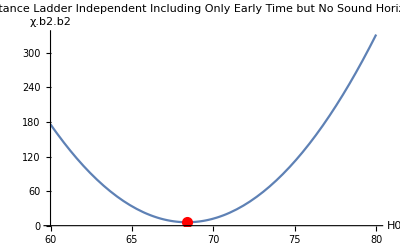

```mathematica
(*Define the chi-square function*)
chiSquare[h0_,data_]:=Sum[((h0-data[[i,2]][[1]])/data[[i,2]][[2]])^2,{i,1,Length[data]}]

(*Function to perform analysis on a dataset*)
analyzeDataset[fullData_,indices_,name_]:=Module[{data,minChiSquare,bestH0,dof,reducedChiSquare,h0Lower,h0Upper},(*Select the specified data points*)data=fullData[[indices]];
{minChiSquare,bestH0Rule}=NMinimize[{chiSquare[h0,data],60<=h0<=80},h0];
bestH0=bestH0Rule[[1,2]];(*Use Part to extract the numerical value*)dof=Length[data]-1;
reducedChiSquare=minChiSquare/dof;
deltaChiSquare[h0_]:=chiSquare[h0,data]-minChiSquare;
h0Lower=FindRoot[deltaChiSquare[h0]==1,{h0,bestH0-1}][[1,2]];
h0Upper=FindRoot[deltaChiSquare[h0]==1,{h0,bestH0+1}][[1,2]];
Print[Style[name<>" Dataset Analysis:",Bold,Larger]];
Print["Data points used: ",indices];
Print["Best fit H0: ",Around[bestH0,{bestH0-h0Lower,h0Upper-bestH0}]];
Print["Minimum χ.b2.b2: ",minChiSquare];
Print["Reduced χ.b2.b2: ",reducedChiSquare];
Print["Degrees of freedom: ",dof];
Print[];
Show[Plot[chiSquare[h0,data],{h0,60,80},PlotLabel->name<>": χ.b2.b2 vs H0",AxesLabel->{"H0","χ.b2.b2"},PlotRange->All],Graphics[{Red,PointSize[0.02],Point[{bestH0,minChiSquare}]}]]]

(*Analyze full Distance Ladder Dependent Dataset*)
analyzeDataset[distanceLadderDependent,Range[Length[distanceLadderDependent]],"Full Distance Ladder Dependent"]

(*Analyze subset of Distance Ladder Independent Dataset*)
analyzeDataset[distanceLadderIndependent,{9,26,27},"Subset of Distance Ladder Independent Including Only Early Time but No Sound Horizon"]
```

### Subset All - Exclude Early Time

Full Distance Ladder Dependent Dataset Analysis:

Excluded data points: {}

Number of data points used: 20

Best fit H0: 72.80.50.5

Minimum χ.b2.b2: 9.7132

Reduced χ.b2.b2: 0.511221

Degrees of freedom: 19

-Graphics-

Distance Ladder Independent (excluding Early time (no sound horizon): {9,26,27}) Dataset Analysis:

Excluded data points: {9,26,27,4,5}

Number of data points used: 28

Best fit H0: 68.10.90.9

Minimum χ.b2.b2: 22.4976

Reduced χ.b2.b2: 0.833244

Degrees of freedom: 27

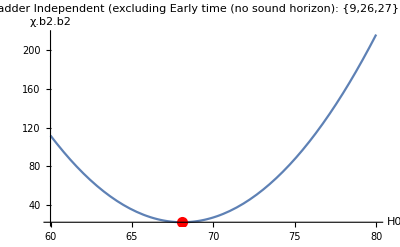

```mathematica
(*Define the chi-square function*)
chiSquare[h0_,data_]:=Sum[((h0-data[[i,2]][[1]])/data[[i,2]][[2]])^2,{i,1,Length[data]}]

(*Function to perform analysis on a dataset*)
analyzeDataset[fullData_,excludeIndices_,name_]:=Module[{data,minChiSquare,bestH0,dof,reducedChiSquare,h0Lower,h0Upper},(*Remove the specified data points*)data=Delete[fullData,List/@excludeIndices];
{minChiSquare,bestH0Rule}=NMinimize[{chiSquare[h0,data],60<=h0<=80},h0];
bestH0=bestH0Rule[[1,2]];(*Use Part to extract the numerical value*)dof=Length[data]-1;
reducedChiSquare=minChiSquare/dof;
deltaChiSquare[h0_]:=chiSquare[h0,data]-minChiSquare;
h0Lower=FindRoot[deltaChiSquare[h0]==1,{h0,bestH0-1}][[1,2]];
h0Upper=FindRoot[deltaChiSquare[h0]==1,{h0,bestH0+1}][[1,2]];
Print[Style[name<>" Dataset Analysis:",Bold,Larger]];
Print["Excluded data points: ",excludeIndices];
Print["Number of data points used: ",Length[data]];
Print["Best fit H0: ",Around[bestH0,{bestH0-h0Lower,h0Upper-bestH0}]];
Print["Minimum χ.b2.b2: ",minChiSquare];
Print["Reduced χ.b2.b2: ",reducedChiSquare];
Print["Degrees of freedom: ",dof];
Print[];
Show[Plot[chiSquare[h0,data],{h0,60,80},PlotLabel->name<>": χ.b2.b2 vs H0",AxesLabel->{"H0","χ.b2.b2"},PlotRange->All],Graphics[{Red,PointSize[0.02],Point[{bestH0,minChiSquare}]}]]]

(*Example usage*)
(*Analyze full Distance Ladder Dependent Dataset*)
analyzeDataset[distanceLadderDependent,{},"Full Distance Ladder Dependent"]

(*Analyze Distance Ladder Independent Dataset excluding Megamasers points 2,3,5 *)
analyzeDataset[distanceLadderIndependent,{9,26,27,4,5},"Distance Ladder Independent (excluding Early time (no sound horizon): {9,26,27})"]
```